## Rotational bands in 165Tm

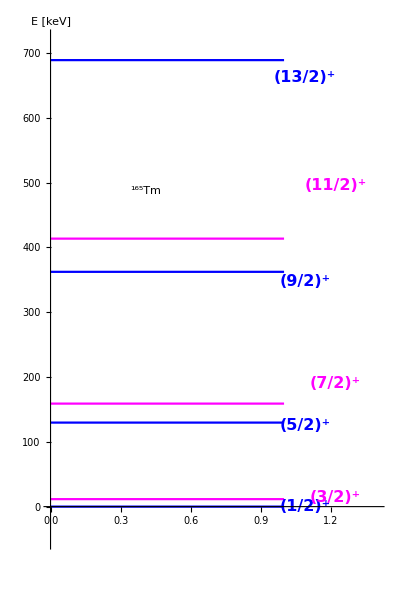

```mathematica
energies=Sort[{688.92,413.49,362.26,158.93,129.63,11.54,0.0}];
spins=Sort[Table[s,{s,1/2,(2*Length[energies]-1)/2,1}]];
A="165";
element="Tm";
plotName=StringTemplate["/Users/basavyr/Documents/Work/DFT/mathematica-useful-algorithms/Physics/rotational-bands-nuclei/````-Rotational-Bands.pdf"][element,A];
energyLevels[spins_,levels_]:=Plot[{Table[energies[[i]],{i,1,Length[energies],2}],Table[energies[[i]],{i,2,Length[energies],2}]},{x,0,1},Axes->{False,True},AspectRatio->1.5,AxesStyle->Directive[Black,Thick],PlotStyle->{Blue,Magenta},PlotRange->{{0,1.4},{-50,720}},AxesLabel->{"","E [keV]"},LabelStyle->{20,Black,Bold,FontFamily->"Arial"},Epilog->{Table[Inset[Style[Superscript[spins[[i]],"+"],16,Blue,Bold,FontFamily->"Arial"],{1.09,0.96levels[[i]]}],{i,1,Length[levels],2}],Table[Inset[Style[Superscript[spins[[i]],"+"],16,Magenta,Bold,FontFamily->"Arial"],{1.22,1.2levels[[i]]}],{i,2,Length[levels],2}],Inset[Framed[Style[Row[{Superscript["",A],element}],Black,Bold,18]],Scaled[{0.3,0.69}]]}];
graf=energyLevels[spins,energies];
Show[graf]
Export[plotName,graf];
```